```mathematica
DataStatistic[x_List]:=Module[{mean,tValue=1.14,deltaB=0.00095,uncertainty},MeanStandardDeviation[data_]:=StandardDeviation[data]/Sqrt[Length[data]];
DeltaA[data_,t_]:=t*StandardDeviation[data];
Uncertainty[data_,t_,deltaB_]:=Sqrt[DeltaA[data,t]^2+deltaB^2];mean=Mean[x];
uncertainty=Uncertainty[x,tValue,deltaB];
Print["Mean: ",mean];
Print["Standard Deviation: ",StandardDeviation[x]];
Print["Mean Standard Deviation: ",MeanStandardDeviation[x]];
Print["deltaA: ",DeltaA[x,tValue]];
Print["deltaB: ",deltaB];
Print["Uncertainty: ",uncertainty];
Return[Around[mean,uncertainty]]];

ShowFitPlot[dataX_List,dataY_List,xName_,yName_,plotName_]:=Module[{data,fitModel},data=Transpose[{dataX,dataY}];
fitModel=LinearModelFit[data,x,x];
Print["Best Fit Equation: ",fitModel["BestFit"]];
Print[Show[ListPlot[data,PlotStyle->Red,PlotLabel->plotName,AxesLabel->{xName,yName}],Plot[fitModel[x],{x,Min[dataX],Max[dataX]}]]];
Return[fitModel["BestFitParameters"]]];
ShowFitPlot[dataX_List,dataY_List,xName_,yName_]:=ShowFitPlot[dataX,dataY,xName,yName,""];
ShowFitPlot[dataX_List,dataY_List]:=ShowFitPlot[dataX,dataY,"","",""];
```

```mathematica
L1=66.15
```

66.15

```mathematica
L2=1.992
```

1.992

```mathematica
L=67.15
```

67.15

```mathematica
datat05={5,4,5,4,5}*0.001+3.28
```

{3.285,3.284,3.285,3.284,3.285}

```mathematica
datat10={1,-1,1,0,0}*0.001+3.29
```

{3.291,3.289,3.291,3.29,3.29}

```mathematica
datat15={-2,1,-1,-2,1}*0.001+3.30
```

{3.298,3.301,3.299,3.298,3.301}

```mathematica
datat20={-2,0,-2,-3,-2}*0.001+3.31
```

{3.308,3.31,3.308,3.307,3.308}

```mathematica
datat25={1,1,3,1,3}*0.001+3.32
```

{3.321,3.321,3.323,3.321,3.323}

```mathematica
datat30={10,6,9,7,9}*0.001+3.32
```

{3.33,3.326,3.329,3.327,3.329}

```mathematica
T05=DataStatistic[datat05]
```

Mean: 3.2846

Standard Deviation: 0.000547723

Mean Standard Deviation: 0.000244949

deltaA: 0.000624404

deltaB: 0.00095

Uncertainty: 0.00113683

3.28460.0011

```mathematica
T10=DataStatistic[datat10]
```

Mean: 3.2902

Standard Deviation: 0.00083666

Mean Standard Deviation: 0.000374166

deltaA: 0.000953792

deltaB: 0.00095

Uncertainty: 0.00134619

3.29020.0013

```mathematica
T15=DataStatistic[datat15]
```

Mean: 3.2994

Standard Deviation: 0.00151658

Mean Standard Deviation: 0.000678233

deltaA: 0.0017289

deltaB: 0.00095

Uncertainty: 0.00197271

3.29940.0020

```mathematica
T20=DataStatistic[datat20]
```

Mean: 3.3082

Standard Deviation: 0.00109545

Mean Standard Deviation: 0.000489898

deltaA: 0.00124881

deltaB: 0.00095

Uncertainty: 0.00156908

3.30820.0016

```mathematica
T25=DataStatistic[datat25]
```

Mean: 3.3218

Standard Deviation: 0.00109545

Mean Standard Deviation: 0.000489898

deltaA: 0.00124881

deltaB: 0.00095

Uncertainty: 0.00156908

3.32180.0016

```mathematica
T30=DataStatistic[datat30]
```

Mean: 3.3282

Standard Deviation: 0.00164317

Mean Standard Deviation: 0.000734847

deltaA: 0.00187321

deltaB: 0.00095

Uncertainty: 0.00210034

3.32820.0021

Best Fit Equation: 3.27324+0.00183771 x

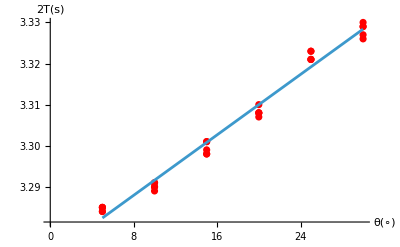

1.63662

```mathematica
t0=ShowFitPlot[Flatten[Table[Table[i,5],{i,5,30,5}]],Flatten[{datat05,datat10,datat15,datat20,datat25,datat30}],"θ(∘)","2T(s)"][[1]]/2
```

```mathematica
g0=(4Pi^2L)/t0^2
```

9.89715

Best Fit Equation: 3.27403+0.00180567 x

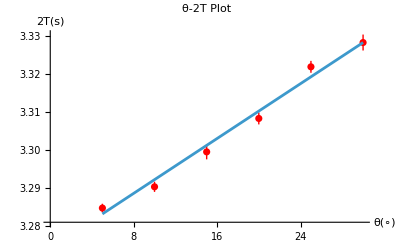

1.63701

```mathematica
T1=ShowFitPlot[Table[i,{i,5,30,5}],{T05,T10,T15,T20,T25,T30},"θ(∘)","2T(s)","θ-2T Plot"][[1]]/2
```

```mathematica
g1=(4Pi^2L)/T1^2
```

9.8924